# Zeroth order Bessel Functions

## Zeroth order Bessel equation and Bessel functions

### Zeroth order Bessel functions arise in solving differential equations for systems with cylindrical symmetry, with no dependence on angular position θ. J_0(z) is often called the zeroth order Bessel function of the first kind, or simply the Bessel function. Y_0(z) is referred to as the zeroth order Bessel function of the second kind. ◼ BesselJ[0, z] gives the zeroth order Bessel function of the first kind, J_0(z). ◼ BesselY[0, z] gives the zeroth order Bessel function of the second kind, Y_0(z). The zeroth order Bessel functions J_0(z) and Y_0(z) are linearly independent solutions to the Bessel equation with n=0 z^2(ϕ̄)_0''+z(ϕ̄)_0'+z^2(ϕ̄)_0=0. That is, (ϕ̄)_0(z) = A_0*J_0(z) + B_0*Y_0(z).

## Properties of Zeroth order Bessel functions ⇒ Plots ⇒ Behavior at z=0.

### Zeroth order Bessel function of the first kind. J_0(z) is regular at z=0. At z=0, J_0(0)=1

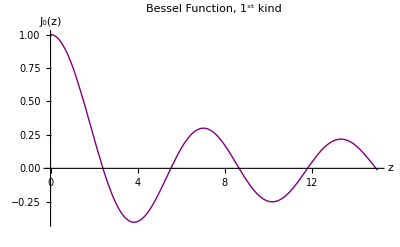

```mathematica
Plot[{BesselJ[0,z]},{z,0,15},PlotLabel->"Bessel Function, 1^st kind",AxesLabel->{"z","J_0(z)"},PlotStyle->{Directive[Purple,Thick]},BaseStyle->{FontSize->14}]
```

### Zeroth order Bessel function of the second kind. Y_0(z) has a logarithmic divergence at z=0. ⇒ For problems that contain z=0 in their domain, with a finiteness condition lim_(z→0) |(ϕ̄)_n(z)|<∞ , the coefficient of the Y_0(z) terms must equal zero.

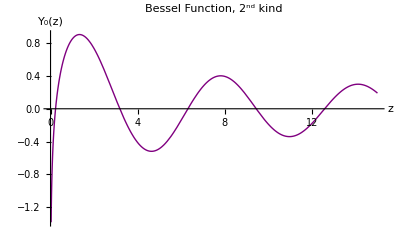

```mathematica
Plot[{BesselY[0,z]+BesselJ[0,z]},{z,0,15},PlotLabel->"Bessel Function, 2^nd kind",AxesLabel->{"z","Y_0(z)"},PlotStyle->{Directive[Purple,Thick]},BaseStyle->{FontSize->14}]
```

## Properties of Zeroth order Bessel functions ⇒ Oscillatory behavior ⇒ Zeros

### Zeroth order Bessel function of the first kind. J_0(z) is oscillatory ⇒ There are an infinite number of solution for J_0(z)=0, yielding an infinite number of eigenfunctions required by the S.L. eigenvalue problem theorem for the disk problem. ⇒ Denote the k^th root of J_0(z) as z_(0 k). Therefore, J_0(z_(0 k))=0. ⇒ Mathematica has a built-in function to find the roots, z_(0 k) = BesselJzero[0,k]. The first few roots are given in the table.

```mathematica
TableForm[Table[{k,N[BesselJZero[0,k]]},{k,1,4}],TableHeadings->{{},{"k","z_(0  k)"}}]
```

| k | z_(0  k)
 | 1 | 2.40483
 | 2 | 5.52008
 | 3 | 8.65373
 | 4 | 11.7915

### Zeroth order Bessel function of the second kind. Y_0(z) is oscillatory ⇒ There are an infinite number of solution for Y_0(z)=0. ⇒ Denote the k^th root of Y_0(z) as s_(0 k). Therefore, Y_0(s_(0 k))=0. ⇒ Mathematica has a built-in function to find the roots, s_(0 k) = BesselYzero[0,k]. The first few roots are given in the table.

```mathematica
TableForm[Table[{k,N[BesselYZero[0,k]]},{k,1,4}],TableHeadings->{{},{"k","s_(0  k)"}}]
```

| k | s_(0  k)
 | 1 | 0.893577
 | 2 | 3.95768
 | 3 | 7.08605
 | 4 | 10.2223

## Properties of Zeroth order Bessel functions ⇒ Expressions in terms of infinite series ⇒ Asymptotic forms

### Infinite series expressions for J_0(z) and Y_0(z). J_0(z)∼∑_(k=0)^∞ (-1)^k/(k!)^2(x/2)^(2k) Y_0(z)∼lim_(ν→0) (J_ν(x)Cos(νπ)-J_-ν(x))/(Sin(νπ)), with J_ν(z)∼∑_(k=0)^∞ (-1)^k/(k!Γ(ν+k+1))(x/2)^(2k), when ν is not an integer, where Γ is the Gamma function.

### Asymptotic forms for J_0(z) and Y_0(z) for large z ⇒ For large z, the roots are separated by π. That is, z_(0 k+1) - z_(0 k) → π, as k becomes large. J_0(z)∼√(2/(π z))Cos[z - π/4 ] Y_0(z)∼√(2/(π z))Sin[z - π/4 ]

### Asymptotic form of J_0(z) and Y_0(z) for small z ⇒ For small z, J_0(z)~1 and J_0(0)=1 ⇒ For small z, Y_0(z)∼2/π ln(z) and Y_0(0) is infinite. Therefore, Y_0 cannot satisfy the finiteness condition at z=0.

## Properties of Zeroth order Bessel functions ⇒ ORTHOGONALITY

#### The orthogonality+ statement for the axisymmetric circular membrane (from the Sturm-Liouville Theorem) is ∫_0^a rϕ_(0 p)ϕ_(0 q)ⅆr=∫_0^a r J_0(z_(0 p)r/a)J_0(z_(0 q)r/a)ⅆr=0, p≠q The integral ∫_0^a r (J_0(z_(0 p)r/a))^2 ⅆr = (a^2/2[J'_0(z_(0 p))])^2=(a^2/2[J_1(z_(0 p))])^2. The mode shapes for the complete circular membrane involved only the Bessel function of the first kind. Both Bessel functions of the first and second kind are involved for annular membranes.

A few checks on the statement of ORTHOGANALITY.  Show that ∫_0^a rϕ_(0,1)ϕ_(0,3)ⅆr=0 and ∫_0^a rϕ_(0,1)ϕ_(0,1)ⅆr  =(a^2/2[J'_0(z_(0,1))])^2

```mathematica
z01=N[BesselJZero[0,1]];z03=N[BesselJZero[0,3]];
```

```mathematica
∫_0^a r*BesselJ[0,z01*r/a]*BesselJ[0,z03*r/a]ⅆr
```

0.

```mathematica
Chop[∫_0^a r*BesselJ[0,z01*r/a]*BesselJ[0,z01*r/a]ⅆr]
```

0.134757 a^2

```mathematica
DBesselJ[m_,z_]=D[BesselJ[m,z],z];
a^2/2*(DBesselJ[0,z01])^2
```

0.134757 a^2

#### The derivative of J'_0(z)=-J_1(z)

```mathematica
DBesselJ0[z_]=D[BesselJ[0,z], z]
```

-BesselJ[1,z]